```mathematica
ClearAll["Global`*"]
```

### Init

```mathematica
tplus=(mB+mK)^2;
tminus=(mB-mK)^2;
tzero=tplus(1-Sqrt[1-tminus/tplus]);
```

```mathematica
z[t_]=(Sqrt[tplus-t]-Sqrt[tplus-tzero])/(Sqrt[tplus-t]+Sqrt[tplus-tzero]);
```

```mathematica
F[q.b2_,x_]=1/(1-(q.b2)/Subscript[m, R,x]^2)Sum[Subscript[α, k,x](z[q.b2]-z[0])^k,{k,0,2}]//Simplify;
```

```mathematica
formFactors={fplus[q.b2_]:> F[q.b2,fplus], fzero[q.b2_]:> F[q.b2,fzero]};
```

```mathematica
(* all masses (and mass-dimension quantities) in GeV units *)
```

```mathematica
constants = {GevToInverseSec :> 1.5 10^24};
values={Subscript[α, 0,fzero]:>0.329, Subscript[α, 1,fzero]:>0.195,Subscript[α, 2,fzero]:>-0.446,Subscript[α, 0,fplus]:>0.329,Subscript[α, 1,fplus]:>-0.876,Subscript[α, 2,fplus]:>0.006,Subscript[m, R,fzero]:>5.54 , Subscript[m, R,fplus]:>5.325 };
```

```mathematica
masses={MW:>80.38,mW:>80.38,MZ:>91.19,mZ:>91.19,MB:>4.18,mb:>4.18,MC:>1.28,mc:>1.28,MU:>0.0022,mu:>0.0022,MT:>173,mt:>173,MS:>0.095,ms:>0.095,mB:>5.279,mK:>0.4937,mπ:>0.14,mD:>1.86,v:>246,me:>0.000511,mμ:>0.106,mτ:>1.777,MD:>0.0047,md:>0.0047,Γh:>0.013,mBs:>5.367,fBs:>0.227,mBd:>5.280,fBd:>0.188};
ckms={CKM[3,3]:>0.999,Vtb:>0.999,CKM[3,2]:>0.0404,Vts:>0.0404,CKM[2,3]:>0.0412,Vcb:>0.0412,CKM[2,2]:>0.973,Vcs:>0.973, Vtd:> 8.1/1000};
couplings={EL:>Sqrt[4 π*7.297/1000],SW:>Sqrt[0.231],CW:>Sqrt[1-0.231],GF:>1.166*10^(-5),Subscript[α,em]:>7.297*10^-3,alphaem:>7.297*10^-3,alphas:>0.1181,Subscript[X,t]:>1.469,sw.b2:>0.231};
eulergamma={Subscript[γ,E]:>0.5772};
```

```mathematica
datapointsππ=ReadList[File["rate_pipi.dat"],{Real,Real},WordSeparators->{"\t"},RecordSeparators->{"\n"}];
```

ReadList::noopen: Cannot open File[rate_pipi.dat].

```mathematica
datapointsππ={{0.28001323,5.17024*10^(-10)},{0.27784854,1.0525554*10^(-9)},{0.2877911,1.8218304*10^(-9)},{0.30592537,3.3623317*10^(-9)},{0.33365947,5.277515*10^(-9)},{0.3639078,8.283586*10^(-9)},{0.41079497,1.2181233*10^(-8)},{0.47179008,1.7907567*10^(-8)},{0.5560635,2.7178222*10^(-8)},{0.6442094,4.2615103*10^(-8)},{0.73974603,5.5053757*10^(-8)},{0.8280175,9.213942*10^(-8)},{0.8877805,1.6462049*10^(-7)},{0.9437583,3.1379568*10^(-7)},{0.97783643,7.033213*10^(-7)},{1.002676,3.6842826*10^(-7)},{1.036807,1.5896644*10^(-7)},{1.0629779,7.317836*10^(-8)},{1.108985,3.958082*10^(-8)},{1.1371115,2.0074902*10^(-8)},{1.1865596,1.27616815*10^(-8)},{1.2277195,9.23311*10^(-9)},{1.2817607,8.933028*10^(-9)},{1.3385478,1.08358424*10^(-8)},{1.3852515,9.2141486*10^(-9)},{1.47,4.38*10^(-9)},{1.5,2.5269602*10^(-9)},{1.5614661,4.1001567*10^(-9)},{1.6033295,6.6537464*10^(-9)},{1.6742321,7.566051*10^(-9)},{1.7473112,5.4732547*10^(-9)},{1.8077103,3.5941348*10^(-9)},{1.88713,3.25975*10^(-9)},{1.9999999,3.7056085*10^(-9)}};
```

```mathematica
Γϕππ=Interpolation[datapointsππ,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
datapointsKK=ReadList[File["rate_KK.dat"],{Real,Real},WordSeparators->{"\t"},RecordSeparators->{"\n"}];
```

ReadList::noopen: Cannot open File[rate_KK.dat].

```mathematica
datapointsKK={{0.992899,1.39798*10^(-7)},{1.07269,1.07816*10^(-7)},{1.13916,8.87269*10^(-8)},{1.25236,8.04012*10^(-8)},{1.31897,8.56912*10^(-8)},{1.45009,8.02007*10^(-8)},{1.58049,7.26857*10^(-8)}{1.69277,5.42831*10^(-8)},{1.81310,4.18707*10^(-8)},{1.99304,3.44371*10^(-8)}};
```

```mathematica
ΓϕKK=Interpolation[datapointsKK,InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.250016} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.265991} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.250016} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

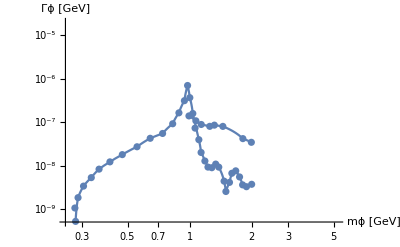

```mathematica
Show[LogLogPlot[{ΓϕKK[mϕ]*HeavisideTheta[mϕ-2mK/.masses]*HeavisideTheta[2-mϕ]},{mϕ,0.25,5.2},PlotRange->{{0.25,5.2},{5*10^(-10),2*10^(-5)}},AxesLabel->{"mϕ [GeV]","Γϕ [GeV]"}],ListPlot[datapointsKK,PlotRange->{5*10^(-10),2*10^(-5)},ScalingFunctions->{"Log","Log"},AxesLabel->{"mϕ [GeV]","Γϕ [GeV]"}],LogLogPlot[Γϕππ[mϕ]*HeavisideTheta[mϕ-2mπ/.masses]*HeavisideTheta[2-mϕ],{mϕ,0.25,5.2},PlotRange->{5*10^(-10),2*10^(-5)},AxesLabel->{"mϕ [GeV]","Γϕ [GeV]"}],ListPlot[datapointsππ,PlotRange->{5*10^(-10),2*10^(-5)},ScalingFunctions->{"Log","Log"},AxesLabel->{"mϕ [GeV]","Γϕ [GeV]"}]]
```

```mathematica
alphaSValues={{1.03,0.49},{1.27,0.40},{1.55,0.34},{2.14,0.28},{3.48,0.23},{6.11,0.19}};
```

```mathematica
AlphaS=Interpolation[alphaSValues,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
Γϕχ[mϕ_,mχ_,ξ_,α_]:=1/(8 π mϕ^2) HeavisideTheta[mϕ-2 mχ] ξ^2 Cos[α]^2 (mϕ^2-4 mχ^2)^(3/2) (* dark fermion *)
Γϕf[mϕ_,α_,mf_]:=HeavisideTheta[mϕ-2 mf] ((mf/v)^2 Sin[α]^2 (mϕ^2-4 mf^2)^(3/2))/(8 π mϕ^2) (* lepton *)
ΓϕW[mϕ_,α_]:=HeavisideTheta[mϕ-2 MW] Sin[α]^2 ((EL)^2 (4 (CW)^4 Sqrt[mϕ^2-4 MW^2] (mϕ^4-4 mϕ^2 MW^2+12 MW^4)))/(64 π (CW)^4 mϕ^2 MW^2 (SW)^2) (* W-boson *)
ΓϕZ[mϕ_,α_]:=HeavisideTheta[mϕ-2 MZ] Sin[α]^2 ((EL)^2 (Sqrt[mϕ^2-4 MZ^2] (CW^4 mϕ^4-4 CW^2 mϕ^2 MW^2+12 MW^4)))/(64 π (CW)^4 mϕ^2 MW^2 (SW)^2) (* Z-boson*)
Γϕγ[MH_,α_]:=Sin[α]^2 (EL^6*(MH^4*(3*MH^2-16*MT^2+18*MW^2)^2+256*MT^4*(MH^2-4*MT^2)^2*ArcTanh[MH/Sqrt[MH^2-4*MT^2]]^4-72*MH^2*MW^2*(MH^2-2*MW^2)*(3*MH^2-16*MT^2+18*MW^2)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^2+81*MW^4*(17*MH^4-64*MH^2*MW^2+64*MW^4)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^4+32*MT^2*(MH^2-4*MT^2)*ArcTanh[MH/Sqrt[MH^2-4*MT^2]]^2*(MH^2*(3*MH^2-16*MT^2+18*MW^2)-36*MW^2*(MH^2-2*MW^2)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^2)))/(18432*MH^5*MW^2*Pi^5*SW^2) (* Photon *)
Γϕg[mϕ_,α_]:=(Sin[α]^2alphas^2mϕ^3)/(32π^3 v^2) Abs[Sum[((mϕ^2/(4mq^2))+((mϕ^2/(4mq^2))-1)*(HeavisideTheta[(mϕ^2/(4mq^2))-1]*(-1/4) (Log[(1+Sqrt[1-1/(mϕ^2/(4mq^2))])/(1-Sqrt[1-1/(mϕ^2/(4mq^2))])]-I π)^2+HeavisideTheta[-(mϕ^2/(4mq^2))+1]ArcSin[Sqrt[(mϕ^2/(4mq^2))]]^2))/((mϕ^2/(4mq^2))^2),{mq,{mu,md,ms,mc,mb,mt}}]]^2*HeavisideTheta[mϕ-2](* gluons *)
Γϕπ[mϕ_,α_]:= Γϕππ[mϕ]*Sin[α]^2*HeavisideTheta[mϕ-2mπ/.masses]*HeavisideTheta[2-mϕ] (* pion *)
ΓϕK[mϕ_,α_]:= ΓϕKK[mϕ]*Sin[α]^2*HeavisideTheta[mϕ-2mK/.masses]*HeavisideTheta[2-mϕ] (* kaon *)
Γϕs[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mK] ((ms/v)^2 Sin[α]^2 (mϕ^2-4 mK^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* strange quarks *)
Γϕc[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mD] ((mc/v)^2 Sin[α]^2 (mϕ^2-4 mD^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* charm quarks *)
Γϕb[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mB] ((mb/v)^2 Sin[α]^2 (mϕ^2-4 mB^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* bottom quarks *)
Γϕmoreπs[mϕ_,α_]:=5.1*10^(-9) Sin[α]^2 mϕ^2 Sqrt[mϕ^2-4mπ^2]*HeavisideTheta[mϕ-4mπ]*HeavisideTheta[2-mϕ] (* additional meson contributions *)
Γϕ[mϕ_,mχ_,ξ_,α_]:=(Γϕχ[mϕ,mχ,ξ,α]+Γϕf[mϕ,α,me]+Γϕf[mϕ,α,mμ]+Γϕf[mϕ,α,mτ]+Γϕπ[mϕ,α]+ΓϕK[mϕ,α]+Γϕmoreπs[mϕ,α]+Γϕg[mϕ,α]+Γϕs[mϕ,α]+Γϕc[mϕ,α]+Γϕb[mϕ,α]+Γϕγ[mϕ,α]+ΓϕW[mϕ,α]+ΓϕZ[mϕ,α])/.{alphas:>AlphaS[mϕ]}/.masses/.couplings
```

```mathematica
Γϕ[1,2,3,4]
```

3.16877×10^-7+0. ⅈ

```mathematica
newWidthsPlot[α_]:=LogLogPlot[{Γϕ[mϕ,1000,0,α],Γϕf[mϕ,α,mμ]/.masses/.couplings,Γϕf[mϕ,α,mτ]/.masses/.couplings,Γϕπ[mϕ,α]/.masses/.couplings,ΓϕK[mϕ,α]/.masses/.couplings,Γϕmoreπs[mϕ,α]/.masses/.couplings,Γϕg[mϕ,α]/.{alphas:>AlphaS[mϕ]}/.masses/.couplings,Γϕs[mϕ,α]/.masses/.couplings,Γϕc[mϕ,α]/.masses/.couplings,Γϕb[mϕ,α]/.masses/.couplings,Γϕγ[mϕ,α]/.masses/.couplings,ΓϕW[mϕ,α]/.masses/.couplings,ΓϕZ[mϕ,α]/.masses/.couplings,Γϕf[mϕ,α,me]/.masses/.couplings},{mϕ,0.25,5.2},AxesLabel->{"mϕ [GeV]","Γϕ [GeV]"},PlotRange->{{0.25,5.2},{5*10^(-10),2*10^(-5)}},PlotLabels->{total,μ μ̄,τ τ̄,ππ,KK,"4π,ηη,ρρ,…",gg,s s̄,c c̄,b b̄,γγ,WW,ZZ,e ē},PlotStyle->{Directive[Dotted,Black],,,,,,,,,,,,,,}]
```

InterpolatingFunction::dmval: Input value {0.250016} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 11 in {931,83,113,657,236,76,141,54,108,25}.

Part::take: Cannot take positions 1 through 12 in {931,83,113,657,236,76,141,54,108,25}.

Part::take: Cannot take positions 1 through 13 in {931,83,113,657,236,76,141,54,108,25}.

General::stop: Further output of Part::take will be suppressed during this calculation.

Callout::copos: {Automatic} is not a valid position for the placement of callouts.

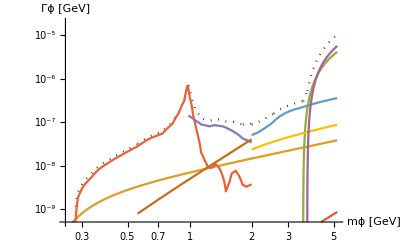

```mathematica
newWidthsPlot[π/2]
```

```mathematica
ContourPlot[(Γϕγ[mϕ,α]/.masses/.couplings)/(Γϕf[mϕ,α,me]/.masses/.couplings),{mϕ,0.0001, 0.001},{α,10^-6,10^-3},ScalingFunctions->{"Log","Log"},Contours->{1},ContourLabels->True,PlotRange->All,PlotLegends->Automatic]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

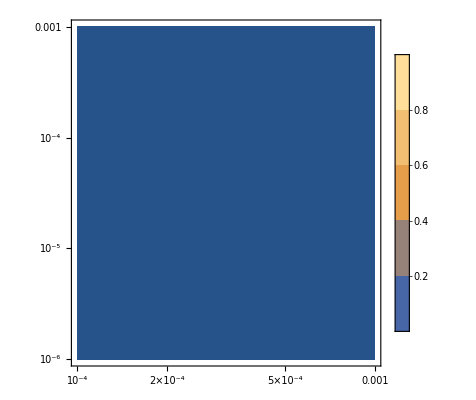

```mathematica
ContourPlot[(Γϕf[mϕ,α,me]/.masses/.couplings),{mϕ,0.0001, 0.001},{α,10^-6,10^-3},ScalingFunctions->{"Log","Log"},ContourLabels->True,PlotRange->Full,PlotLegends->Automatic]
```

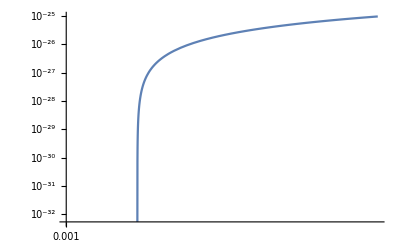

```mathematica
LogLogPlot[{(Γϕf[mϕ,10^-4,me]/.masses/.couplings),(Γϕγ[mϕ,10^-4])},{mϕ,0.001,0.0011},PlotRange->Full]
```

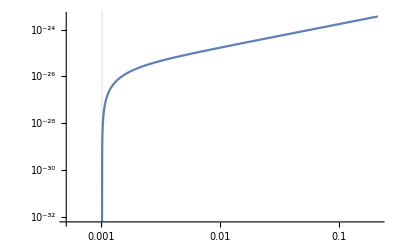

```mathematica
LogLogPlot[(Γϕf[mϕ,10^-5,me]/.masses/.couplings),{mϕ,(me)/.masses,(2 mμ)/.masses},PlotRange->Full,GridLines->{{2 me/.masses},{}}]
```

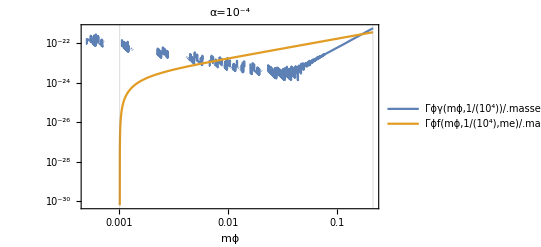

```mathematica
LogLogPlot[{(Γϕγ[mϕ,10^-4]/.masses/.couplings),(Γϕf[mϕ,10^-4,me]/.masses/.couplings)},{mϕ,(me)/.masses,(2mμ)/.masses},PlotRange->Full,GridLines->{{2 me/.masses,2 mμ/.masses},{}}, PlotLegends->"Expressions",Frame->True, FrameLabel->{"mϕ",None}, PlotLabel->"α=10^-4"]
```

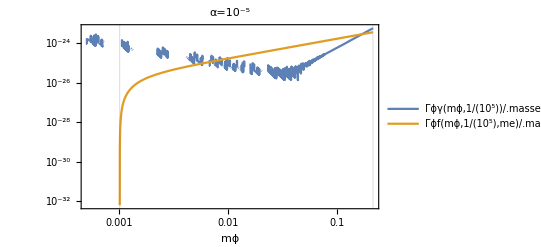

```mathematica
LogLogPlot[{(Γϕγ[mϕ,10^-5]/.masses/.couplings),(Γϕf[mϕ,10^-5,me]/.masses/.couplings)},{mϕ,(me)/.masses,(2mμ)/.masses},PlotRange->Full,GridLines->{{2 me/.masses,2 mμ/.masses},{}}, PlotLegends->"Expressions",Frame->True, FrameLabel->{"mϕ",None}, PlotLabel->"α=10^-5"]
```

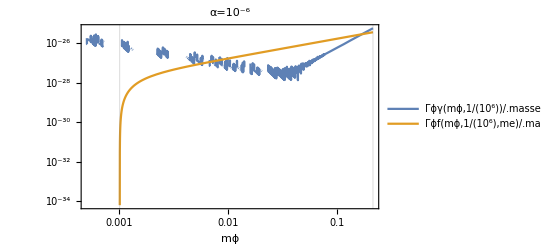

```mathematica
LogLogPlot[{(Γϕγ[mϕ,10^-6]/.masses/.couplings),(Γϕf[mϕ,10^-6,me]/.masses/.couplings)},{mϕ,(me)/.masses,(2mμ)/.masses},PlotRange->Full,GridLines->{{2 me/.masses,2 mμ/.masses},{}}, PlotLegends->"Expressions",Frame->True, FrameLabel->{"mϕ",None}, PlotLabel->"α=10^-6"]
```